```mathematica
Manipulate[Plot[b Cos[theta] + a (Sin[theta])^2, {theta, 0, Pi}], {a, -5, 5}, {b, -5,5}]
```

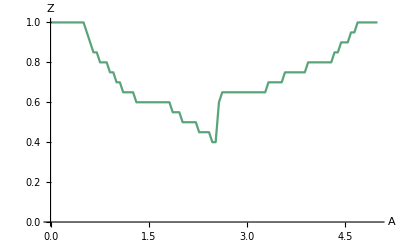

```mathematica
path = "/home/koritskiy/rqc/ferrimagnet/confusion_learning/results/2d/2020-08-03-15:42:18/";
A =Transpose[Import[StringJoin[path , "A.dat"]]][[1]];
b = Transpose[Import[StringJoin[path , "b.dat"]]][[1]];
Z =Flatten[Import[StringJoin[path , "Z.dat"]]];
Final =Table[{A[[i]], Z[[i]]}, {i, 1, Length[A]}];
ListLinePlot[Final, AxesLabel->{"A", "Z"}, ColorFunction->"BlueGreenYellow"]
```